```mathematica
(*BSW-Wulthopp method to numerically solve the 't Hooft eqn.*)
```

```mathematica
(*Mn^2 Subscript[ϕ, n](x) = ((m1^2-β^2)/x+(m2^2-β^2)/(1-x))Subscript[ϕ, n](x)-β^2(∫_0)^1 dy Subscript[ϕ, n](y) PV/(y-x)^2*)
```

```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output"->StandardForm}]
```

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
m1=2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=2*β;
```

```mathematica
(*type in H and V*)
```

```mathematica
HMatx=Table[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
VMatx=Table[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
```

```mathematica
(*solve the eigen problem*)
```

```mathematica
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
```

```mathematica
(*the list of eigenvalues, the first 6 excitations*)
```

```mathematica
Take[√vals β//Sort,{1,12}]
```

{4.69625,5.96609,6.86783,7.64758,8.3299,8.95527,9.52976,10.0692,10.5759,11.0581,11.5169,11.9574}

```mathematica
(*construct the wave functions and plot*)
```

```mathematica
Do[g[j]=Dot[Table[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}]
```

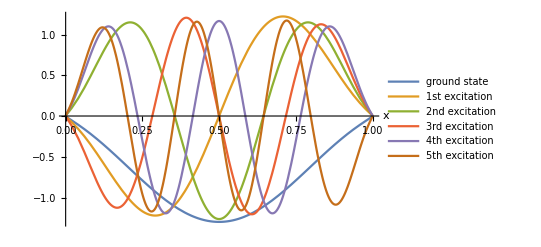

```mathematica
Plot[{g[Nx],g[Nx-1],g[Nx-2],g[Nx-3],g[Nx-4],g[Nx-5]},{x,0,1},AxesLabel->Automatic,PlotLegends->{"ground state","1st excitation","2nd excitation","3rd excitation","4th excitation","5th excitation"},PlotRange->Full]
```

```mathematica
grd=g[Nx]/√NIntegrate[g[Nx]^2,{x,0,1}];
```

```mathematica
ect1=g[Nx-1]/√NIntegrate[g[Nx-1]^2,{x,0,1}];
```

```mathematica
ect2=g[Nx-2]/√NIntegrate[g[Nx-2]^2,{x,0,1}];
```

```mathematica
ect5=g[Nx-5]/√NIntegrate[g[Nx-5]^2,{x,0,1}];
```

```mathematica
ϵ=10^-6;
g1[x_]=grd;
f[x_]:=NIntegrate[g1[y]/(y-x)^2,{y,0,x-ϵ}]+NIntegrate[g1[y]/(y-x)^2,{y,x+ϵ,1}]-2 g1[x]/ϵ
```

```mathematica
LHS1[x_]=((√vals β//Sort)[[1]])^2 grd;
RHS1[x_]:=((m1^2-β^2)/x+(m2^2-β^2)/(1-x))grd-β^2 f[x]
```

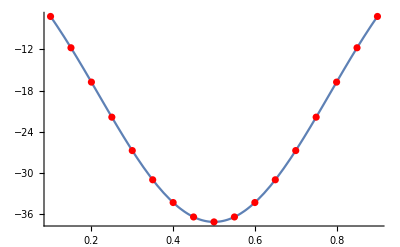

```mathematica
LP1=Plot[{LHS1[x]},{x,0+10^-1,1-10^-1},PlotRange->Full];
RP1=ListPlot[ParallelTable[{x,RHS1[x]},{x,1/20,19/20,1/20}],PlotStyle->Red];
Show[LP1,RP1]
```

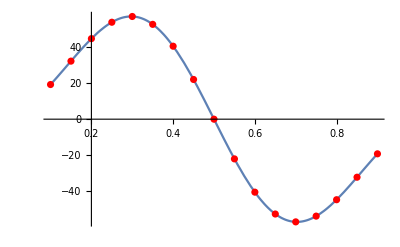

```mathematica
g2[x_]=ect1;
f2[x_]:=NIntegrate[g2[y]/(y-x)^2,{y,0,x-ϵ}]+NIntegrate[g2[y]/(y-x)^2,{y,x+ϵ,1}]-2 g2[x]/ϵ
LHS2[x_]=((√vals β//Sort)[[2]])^2 ect1;
RHS2[x_]:=((m1^2-β^2)/x+(m2^2-β^2)/(1-x))ect1-β^2 f2[x]
LP2=Plot[{LHS2[x]},{x,0+10^-1,1-10^-1},PlotRange->Full];
RP2=ListPlot[ParallelTable[{x,RHS2[x]},{x,1/20,19/20,1/20}],PlotStyle->Red];
Show[LP2,RP2]
```

```mathematica
NIntegrate[(g1[y]-g1[x])/(y-x)^2/.x->0.5,{y,0,1},AccuracyGoal->10]
```

9.75148

```mathematica
NIntegrate[(g1[y]-g1[0.5])/(y-0.5)^2,{y,0,0.5,1},AccuracyGoal->10,Method->PrincipalValue]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3.91316×10^-58}. NIntegrate obtained 4.57942×10^99 and 4.62657×10^99 for the integral and error estimates.

4.57942×10^99

```mathematica
NIntegrate[(g1[y]-g1[0.5]-(y-0.5)(D[g1[x],x]/.x->0.5))/(y-0.5)^2,{y,0,0.5,1},AccuracyGoal->10,Method->PrincipalValue]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3.91316×10^-58}. NIntegrate obtained 4.57942×10^99 and 4.62657×10^99 for the integral and error estimates.

4.57942×10^99